```mathematica
(*Режим непрерывной накчки*)
```

```mathematica
Experiment1=({{"Ток накачки, A", "Напряжение, В", "Показания калориметра, Дж"}, {2.1, 6, 49}, {1.9, 6, 46}, {1.8, 6, 45}, {1.7, 6, 43}, {1.6, 6, 41}, {1.5, 6, 36}, {1.4, 6, 32}, {1.3, 6, 29}, {1.2, 6, 25}, {1.1, 6, 21}, {1.0, 6, 17}});
Experiment1Extended=Append[Transpose[Experiment1],Join[{"Показания ИМЛ, Вт"},N[Experiment1[[2;;12,3]]*270*10^-4]]];
Experiment1Extended=Append[Experiment1Extended,Join[{"W_(:043d:0430:043a:0430:0447:043a:0430), ВТ"},N[Experiment1[[2;;12,1]]*Experiment1[[2;;12,2]]]]];
Experiment1Extended=Transpose[Experiment1Extended];
Grid[Experiment1Extended, Frame->All]
```

Ток накачки, A | Напряжение, В | Показания калориметра, Дж | Показания ИМЛ, Вт | W_накачка, ВТ
2.1 | 6 | 49 | 1.323 | 12.6
1.9 | 6 | 46 | 1.242 | 11.4
1.8 | 6 | 45 | 1.215 | 10.8
1.7 | 6 | 43 | 1.161 | 10.2
1.6 | 6 | 41 | 1.107 | 9.6
1.5 | 6 | 36 | 0.972 | 9.
1.4 | 6 | 32 | 0.864 | 8.4
1.3 | 6 | 29 | 0.783 | 7.8
1.2 | 6 | 25 | 0.675 | 7.2
1.1 | 6 | 21 | 0.567 | 6.6
1. | 6 | 17 | 0.459 | 6.

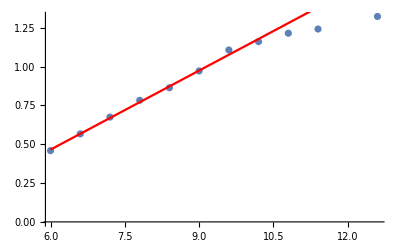

```mathematica
PlotPartExperiment1=Transpose[{Experiment1Extended[[2;;12]][[All,4]]}].({{0, 1}})+Transpose[{Experiment1Extended[[2;;12]][[All,5]]}].({{1, 0}});
PlotPartExperiment1Fit=LinearModelFit[PlotPartExperiment1[[6;;All]],x,x];
Show[ListPlot[PlotPartExperiment1],Plot[PlotPartExperiment1Fit["BestFit"],{x,6,13},PlotStyle->Red]]
```

1.1А
TIME STEP : 125 = 20 us
VOLTAGE STEP : CH1 : 32 = 50 mV
CH2 : 32 = 15 mV

```mathematica
Table11A=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Photonics_Labs/Fiber Laser/654 1.10.2018/1.1A.csv"][[10;;All]];
ListLinePlot[Table11A[[All,1;;2]], PlotRange->Full]
```

Import::nffil: File not found during Import.

Part::take: Cannot take positions 10 through -1 in $Failed.

Part::take: Cannot take positions 1 through 2 in $Failed.

ListLinePlot::lpn: $Failed⟦10;;All⟧⟦All,1;;2⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[$Failed⟦10;;All⟧⟦All,1;;2⟧,PlotRange→Full]

```mathematica
PlotPartExperiment1Fit["BestFit"]
```

-0.552857+0.169714 x

```mathematica
Solve[PlotPartExperiment1Fit["BestFit"]==0,x]
```

{{x→3.25758}}

```mathematica
Table12A=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Photonics_Labs/Fiber Laser/654 1.10.2018/1.2A.csv"][[10;;All]];
ListLinePlot[Table12A[[All,1;;2]], PlotRange->Full]
```

Import::nffil: File not found during Import.

Part::take: Cannot take positions 10 through -1 in $Failed.

Part::take: Cannot take positions 1 through 2 in $Failed.

ListLinePlot::lpn: $Failed⟦10;;All⟧⟦All,1;;2⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[$Failed⟦10;;All⟧⟦All,1;;2⟧,PlotRange→Full]

```mathematica
Render[file_]:=(HeaderLineNum=7;
FooterLineNum=0;
TotalColNum=3;
fileN=OpenRead[StringJoin["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Photonics_Labs/Fiber Laser/654 1.10.2018/",file]];
Skip[fileN,String,HeaderLineNum];
data=ReadList[fileN,Table[Number,{i,1,TotalColNum}]][[;;-(FooterLineNum+1)]];
Close[fileN];
ListLinePlot[data[[All,1;;2]], PlotRange->Full,PlotLabel->StringReplace[file,".txt"-> ""],LabelStyle->{GrayLevel[0]},PlotTheme->"Detailed"]
);
```

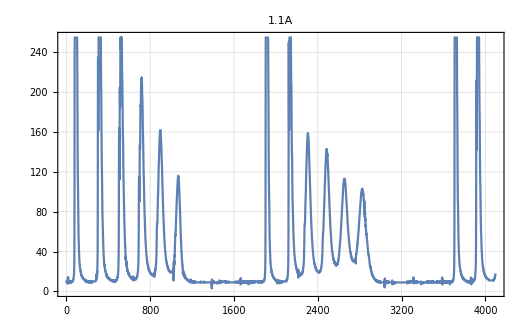

```mathematica
Render["1.1A.txt"]
```

```mathematica
SetDirectory["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Photonics_Labs/Fiber Laser/654 1.10.2018/"];
Sources=FileNames[];
Graphs={};
For[i=1,i≤Length[Sources],i++,
If[FileExtension[Sources[[i]]]=="txt",
SetDirectory["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Photonics_Labs/Fiber Laser"];
Export[StringJoin[StringReplace[Sources[[i]],".txt"-> ""],".pdf"],Render[Sources[[i]]]]
]
]
```